```mathematica
Integrate[1/(x/c+1)^2,x]
```

-c^2/(c+x)

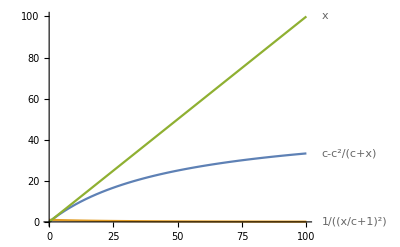

```mathematica
Block[{c=50},Plot[{c-c^2/(c+x),1/(x/c +1)^2,x},{x,0,100},PlotLabels->"Expressions"]]
```

```mathematica
Limit[c-c^2/(c+x),x->Infinity]
```

c

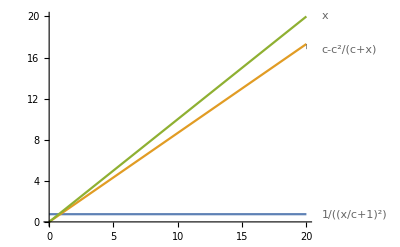

```mathematica
Block[{k = 3/4,c=x/(Sqrt[1/k]-1)},Plot[{1/((x/c)+1)^2,c-c^2/(c+x),x},{x,0,20},PlotLabels->"Expressions"]]
```

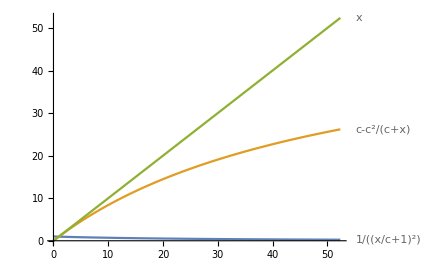
{-Graphics-,52.3861,4.56435}

```mathematica
Block[{b = 5, k = 5/6,c=b/(Sqrt[1/k]-1)},{Plot[{1/((x/c)+1)^2,c-c^2/(c+x),x},{x,0,c},PlotLabels->"Expressions"],N[c],Block[{x=b},N[c-c^2/(c+x)]]}]
```

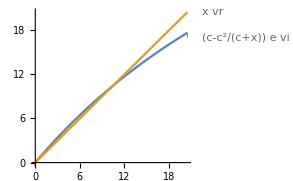
{-Graphics-,{{x→0},{x→10.4772}},52.3861,8.73102}

```mathematica
Block[{vr= 1, vi = 1.0,e=1.2, b = 5, k = 5/6,c=b/(Sqrt[1/k]-1), slv = Solve[(c-c^2/(c+x))*e*vi == x*vr,x]}, {Plot[{(c-c^2/(c+x))*e*vi , x*vr},{x,0,Replace[x,slv[[2]] ] + 10},PlotLabels->"Expressions"],slv, N[c], N[c-c^2/(c+x)/.slv[[2]]]}]
```

```mathematica
Solve[(c-c^2/(c+x))*e*vi == x*vr,x]
```

{{x→0},{x→(c (e vi-vr))/vr}}